```mathematica
f[x_,u_,s_]:=Exp[-(x-u)^2/(2*s^2)]/(Sqrt[2*Pi]*s)
```

```mathematica
f[1,1,1]
```

1/(2 π Sqrt)

```mathematica
g1[x_]:=0.5*f[x,0,1]
```

```mathematica
g2[x_]:=0.5*f[x,3,Sqrt[3]]
```

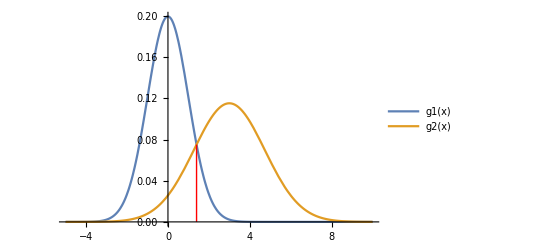

```mathematica
Plot[{g1[x],g2[x]},{x,-5,10},PlotLegends->"Expressions",Epilog->{Red,Line[{{1.39792,0},{1.39792,g1[1.39792]}}]}]
```

```mathematica
Solve[g1[x]==g2[x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→-4.39792,x2→-4.39792},{x1→1.39792,x2→-4.39792},{x1→-4.39792,x2→1.39792},{x1→1.39792,x2→1.39792}}